```mathematica
freq=578
c=0.18277628660756454
a=0.24
nTerms=40
k=Sqrt[freq/c]
d=0.025/a
```

1223

0.2

0.24

40

78.1985

81.9

0.104167

```mathematica
kn[n1_,n2_]:=(Pi/a)*Sqrt[n1^2+n2^2]
mode[x_,y_,n1_,n2_]:=(2/a)*Cos[n1*Pi*x/a]*Cos[n2*Pi*y/a]
```

```mathematica
An[k_,d_,n1_,n2_]:=mode[a/2,a/2,n1,n2]/((k^2-kn[n1,n2]^2)+(2*I*d*k))
norm=Sqrt[Sum[Abs[An[k,d,n1,n2]]^2,{n1,1,nTerms},{n2,1,nTerms}]]
an[k_,d_,n1_,n2_]:=An[k,d,n1,n2]/norm
```

0.0806999

```mathematica
Ψ[x_,y_]:=Sum[an[k,d,n1,n2]*mode[x,y,n1,n2],{n1,0,nTerms},{n2,0,nTerms}]
```

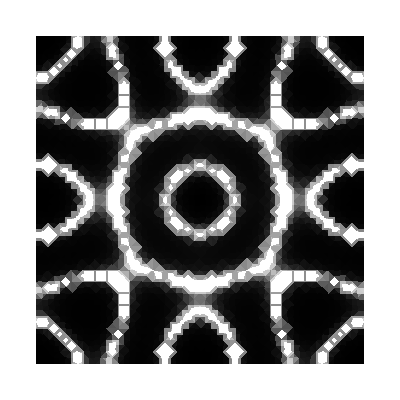

```mathematica
p=DensityPlot[1/Abs[Ψ[x,y]]^2,{x,0,a},{y,0,a},ColorFunction->GrayLevel,MaxRecursion->Automatic,Frame->None]
```

```mathematica
Sqrt[1940/.2881]
```

82.0596

```mathematica
Sqrt[1600/.237]
```

82.1648

```mathematica
1223/81.8^2
```

0.182776